# 3-band dispersive: self-consistency, Ds and Tc

### Def: bloch state

```mathematica
a[J_,m_,k_,phi_]:=k^J Cos[J phi]
```

```mathematica
b[J_,m_,k_,phi_]:=k^J Sin[J phi]
```

Bloch states:

```mathematica
uplus[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2)(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2))^(-1/2){a[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)-I b[J,m,k,phi]m,a[J,m,k,phi]^2+b[J,m,k,phi]^2,b[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)+I a[J,m,k,phi]m}
```

```mathematica
uplusdag[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2)(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2))^(-1/2){a[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)+I b[J,m,k,phi]m,a[J,m,k,phi]^2+b[J,m,k,phi]^2,b[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)-I a[J,m,k,phi]m}
```

```mathematica
u0[J_,m_,k_,phi_]:=(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(-1/2){-b[J,m,k,phi],I m,a[J,m,k,phi]}
```

```mathematica
u0dag[J_,m_,k_,phi_]:=(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(-1/2){-b[J,m,k,phi],-I m,a[J,m,k,phi]}
```

```mathematica
uminus[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2)(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2))^(-1/2){-a[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)-I b[J,m,k,phi]m,a[J,m,k,phi]^2+b[J,m,k,phi]^2,-b[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)+I a[J,m,k,phi]m}
```

```mathematica
uminusdag[J_,m_,k_,phi_]:=(2(a[J,m,k,phi]^2+b[J,m,k,phi]^2)(a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2))^(-1/2){-a[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)+I b[J,m,k,phi]m,a[J,m,k,phi]^2+b[J,m,k,phi]^2,-b[J,m,k,phi](a[J,m,k,phi]^2+b[J,m,k,phi]^2+m^2)^(1/2)-I a[J,m,k,phi]m}
```

### Def: quasiparticle energy

quasiparticle band at μ=0:

```mathematica
edisp3band[J_,m_,k_]:=Sqrt[k^(2J)+m^2]
```

```mathematica
quasiplus[J_,m_,k_,delta_]:=Sqrt[edisp3band[J,m,k]^2+delta^2]
```

```mathematica
quasi0[J_,m_,k_,delta_]:=delta
```

```mathematica
quasiminus[J_,m_,k_,delta_]:=Sqrt[edisp3band[J,m,k]^2+delta^2]
```

## secant to solve gap equation

### Def: gap eq at T=0

compute U from the gap equation

```mathematica
ua3band[J_,m_]:=(
integral=(1/(2π)^2)NIntegrate[k (Abs[uplus[J,m,k,phi][[1]]]^2/(2quasiplus[J,m,k,delta])+Abs[u0[J,m,k,phi][[1]]]^2/(2quasi0[J,m,k,delta])+Abs[uminus[J,m,k,phi][[1]]]^2/(2quasiminus[J,m,k,delta])),{phi,0,2π},{k,0,1}];
1/integral
)
```

```mathematica
ub3band[J_,m_]:=(
integral=(1/(2π)^2)NIntegrate[k (Abs[uplus[J,m,k,phi][[2]]]^2/(2quasiplus[J,m,k,delta])+Abs[u0[J,m,k,phi][[2]]]^2/(2quasi0[J,m,k,delta])+Abs[uminus[J,m,k,phi][[2]]]^2/(2quasiminus[J,m,k,delta])),{phi,0,2π},{k,0,1}];
1/integral
)
```

### calculation

```mathematica
J=1;delta=0.01;
mlist=Table[0.001(i-1)+0.0001,{i,1,51}];
ualist={};
ublist={};
For[i=1,i<Length@mlist+1,i++,
m=mlist[[i]];
uavalue=ua3band[J,m];
ubvalue=ub3band[J,m];
AppendTo[ualist,uavalue];
AppendTo[ublist,ubvalue];
];
dataA=Table[{mlist[[i]]/delta,ualist[[i]]/delta},{i,1,Length@mlist}];
dataB=Table[{mlist[[i]]/delta,ublist[[i]]/delta},{i,1,Length@mlist}];
```

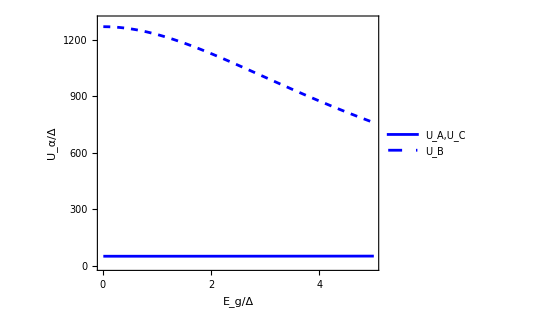

```mathematica
small3band=ListPlot[{dataA,dataB},Joined->True,PlotRange->{{0,5},{0,1300}},
PlotStyle->{Blue,{Blue,Dashed}},
LabelStyle->Directive[Black,18],
Frame->True,
FrameTicks->{{{0,300,600,900,1200},None},{{0,1,2,3,4,5},None}},FrameStyle->Directive[Black,Thickness[0.005]],
FrameLabel->{"E_g/Δ","U_α/Δ"},
PlotLegends->Placed[LineLegend[{Style["U_A,U_C",15],Style["U_B",15]},LegendLayout->"Row"], {0.5,0.2}],
AspectRatio->0.8,
ImageSize->400,(*PlotRangePadding->{Scaled[.01],0},*)ImagePadding->70]
```

```mathematica
J=1;delta=0.1;
mlist=Table[0.01(i-1)+0.001,{i,1,51}];
ualist={};
ublist={};
(*uclist={};*)
For[i=1,i<Length@mlist+1,i++,
m=mlist[[i]];
uavalue=ua3band[J,m];
ubvalue=ub3band[J,m];
(*ucvalue=uc[J,m];*)
AppendTo[ualist,uavalue];
AppendTo[ublist,ubvalue];
(*AppendTo[uclist,ucvalue];*)
];
dataA=Table[{mlist[[i]]/delta,ualist[[i]]/delta},{i,1,Length@mlist}];
dataB=Table[{mlist[[i]]/delta,ublist[[i]]/delta},{i,1,Length@mlist}];
(*dataC=Table[{mlist[[i]]/delta,uclist[[i]]/delta},{i,1,Length@mlist}];*)
```

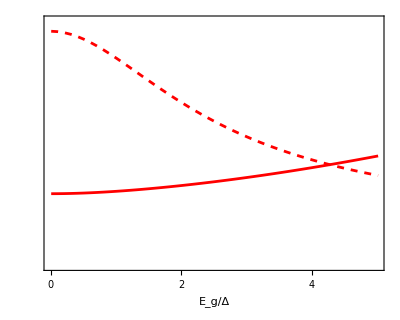

```mathematica
large3band=ListPlot[{dataA,dataB},Joined->True,PlotRange->{{0,5},{0,145}},
PlotStyle->{Red,{Red,Dashed}},
LabelStyle->Directive[Black,18],
Frame->True,FrameTicks->{{None,{0,30,60,90,120}},{{0,1,2,3,4,5},None}},FrameStyle->Directive[Black,Thickness[0.005]],
FrameLabel->{"E_g/Δ",""},
(*PlotLegends->Placed[{"U_A","U_B"}, {0.3,0.8}],*)
AspectRatio->0.8,
ImageSize->400,(*PlotRangePadding->{Scaled[.01],0},*)ImagePadding->70]
```

```mathematica
uplot3band=Overlay[{small3band,large3band}]
```

-Graphics--Graphics-

```mathematica
Export["3bandU.pdf",uplot3band]
```

3bandU.pdf

```mathematica
J=1;delta=0.001;
mlist=Table[0.0002(i-1)+0.0001,{i,1,51}];
ualist={};
ublist={};
(*uclist={};*)
For[i=1,i<Length@mlist+1,i++,
m=mlist[[i]];
uavalue=ua3band[J,m];
ubvalue=ub3band[J,m];
(*ucvalue=uc[J,m];*)
AppendTo[ualist,uavalue];
AppendTo[ublist,ubvalue];
(*AppendTo[uclist,ucvalue];*)
];
dataA=Table[{mlist[[i]]/delta,ualist[[i]]/delta},{i,1,Length@mlist}];
dataB=Table[{mlist[[i]]/delta,ublist[[i]]/delta},{i,1,Length@mlist}];
(*dataC=Table[{mlist[[i]]/delta,uclist[[i]]/delta},{i,1,Length@mlist}];*)
```

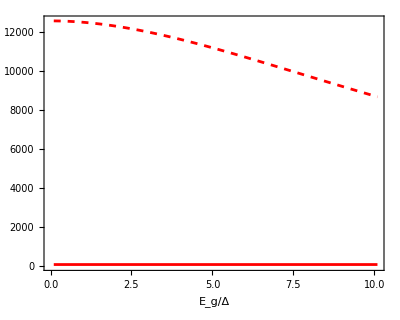

```mathematica
large3band=ListPlot[{dataA,dataB},Joined->True,(*PlotRange->{{0,5},{0,145}},*)
PlotStyle->{Red,{Red,Dashed}},
LabelStyle->Directive[Black,18],
Frame->True,(*FrameTicks->{{None,{0,30,60,90,120}},{{0,1,2,3,4,5},None}},*)FrameStyle->Directive[Black,Thickness[0.005]],
FrameLabel->{"E_g/Δ",""},
(*PlotLegends->Placed[{"U_A","U_B"}, {0.3,0.8}],*)
AspectRatio->0.8,
ImageSize->400,(*PlotRangePadding->{Scaled[.01],0},*)ImagePadding->70]
```

### Def: secant method solve Δ from fixed U_A, U_B at finite T

```mathematica
newtonA3band[deltaA_?NumericQ,deltaB_?NumericQ,temp_,uA_,uB_]:=(
deltaavg=(2deltaA+deltaB)/3;
integral=(uA/(2π)^2)deltaavg NIntegrate[k (Abs[uplus[J,m,k,phi][[1]]]^2 Tanh[quasiplus[J,m,k,deltaavg]/(2temp)]/(2quasiplus[J,m,k,deltaavg])+Abs[u0[J,m,k,phi][[1]]]^2Tanh[quasi0[J,m,k,deltaavg]/(2temp)]/(2quasi0[J,m,k,deltaavg])+Abs[uminus[J,m,k,phi][[1]]]^2Tanh[quasiminus[J,m,k,deltaavg]/(2temp)]/(2quasiminus[J,m,k,deltaavg])),{phi,0,2π},{k,0,1}]-deltaA
)
```

```mathematica
newtonB3band[deltaA_?NumericQ,deltaB_?NumericQ,temp_,uA_,uB_]:=(
deltaavg=(2deltaA+deltaB)/3;
integral=(uB/(2π)^2)deltaavg NIntegrate[k (Abs[uplus[J,m,k,phi][[2]]]^2 Tanh[quasiplus[J,m,k,deltaavg]/(2temp)]/(2quasiplus[J,m,k,deltaavg])+Abs[u0[J,m,k,phi][[2]]]^2Tanh[quasi0[J,m,k,deltaavg]/(2temp)]/(2quasi0[J,m,k,deltaavg])+Abs[uminus[J,m,k,phi][[2]]]^2Tanh[quasiminus[J,m,k,deltaavg]/(2temp)]/(2quasiminus[J,m,k,deltaavg])),{phi,0,2π},{k,0,1}]-deltaB
)
```

```mathematica
secant3bandstep[{deltaA0_,deltaB0_},{deltaA1_,deltaB1_}]:=(
input0={deltaA0,deltaB0};
input1={deltaA1,deltaB1};
functionlist={newtonA3band,newtonB3band};
jacobian=ConstantArray[0,{2,2}];
For[i=1,i<3,i++,
For[j=1,j<3,j++,changelist1=input1;changelist1[[j]]=input0[[j]];
jacobian[[i,j]]=(functionlist[[i]][changelist1[[1]],changelist1[[2]],temp,uA,uB]-functionlist[[i]][input1[[1]],input1[[2]],temp,uA,uB])/(changelist1[[j]]-input1[[j]]);
];
];
outputlist0=input1;
inversejacob=Inverse[jacobian];
(*Print["The min element of jacobian is ",Min[Abs[jacobian]]];
Print["The max element of inverse jacobian is ",Max[Abs[inversejacob]]];*)
inversetimes=inversejacob.Table[functionlist[[k]][input1[[1]],input1[[2]],temp,uA,uB],{k,1,2}];
alpha=1/(1+10Norm[inversetimes]);
(*Print["The damping factor is ",alpha];*)
outputlist1=input1-alpha*inversetimes;
)
```

```mathematica
secant3band[inputdeltaA_,inputdeltaB_]:=(
alpha=0.1;
outputlist1={inputdeltaA,inputdeltaB};
outputlist0=outputlist1+0.001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.95,secant3bandstep[outputlist0,outputlist1];];
deltaA=outputlist1[[1]];
deltaB=outputlist1[[2]];
)
```

## Ds vs m calculation

### Def: quantum metric

choose c(m)=m:

```mathematica
(* QM of the middle band*)
g0xx[J_,m_,k_]:=J^2 k^(2J-2)(m^2+k^(2J)/2)/(m^2+k^(2J))^2
```

### Def: Ds at T=0, numerical (μ=0):

```mathematica
(*the x direction has been averaged*)
vsquare3band[J_,m_,k_]:=(1/2)J^2k^(4J-2)/(m^2+k^(2J))
```

the integral below excludes a factor Δ:

```mathematica
(*the T=0 function is in unit of delta, while the finite-T one is not, careful!*)
```

```mathematica
ds3band[J_?NumericQ,m_?NumericQ,delta_?NumericQ]:=2NIntegrate[(k/(2π))(delta/quasiplus[J,m,k,delta]^3)vsquare3band[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]+4NIntegrate[(k/(2π))(1-delta/quasiplus[J,m,k,delta])g0xx[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

### Def: Ds of finite temp (for μ=0 only)

coherence factors:

between 0 and up band:

```mathematica
p0upplus[J_,m_,k_,deltat_]:=(1/2)(1+delta/quasiplus[J,m,k,deltat])
```

```mathematica
p0upminus[J_,m_,k_,deltat_]:=(1/2)(1-delta/quasiplus[J,m,k,deltat])
```

```mathematica
ds3bandtemp[J_?NumericQ,m_?NumericQ,deltat_?NumericQ,temp_?NumericQ]:=2deltat^2 NIntegrate[(k/(2π))(vsquare3band[J,m,k]/quasiplus[J,m,k,deltat]^3)(Tanh[quasiplus[J,m,k,deltat]/(2temp)]-(quasiplus[J,m,k,deltat]/(2temp))Sech[quasiplus[J,m,k,deltat]/(2temp)]^2),{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]+4deltat^2NIntegrate[(k/(2π))(Tanh[quasi0[J,m,k,deltat]/(2temp)]/quasi0[J,m,k,deltat]+Tanh[quasiplus[J,m,k,deltat]/(2temp)]/quasiplus[J,m,k,deltat]-2p0upplus[J,m,k,deltat](Tanh[quasi0[J,m,k,deltat]/(2temp)]+Tanh[quasiplus[J,m,k,deltat]/(2temp)])/(quasi0[J,m,k,deltat]+quasiplus[J,m,k,deltat])-2p0upminus[J,m,k,deltat](Tanh[quasi0[J,m,k,deltat]/(2temp)]-Tanh[quasiplus[J,m,k,deltat]/(2temp)])/(quasi0[J,m,k,deltat]-quasiplus[J,m,k,deltat]))g0xx[J,m,k],{k,0,1},PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->500,Method->"GlobalAdaptive"]
```

test the function ds3bandftemp (compare with the T=0 function ds3bandf):

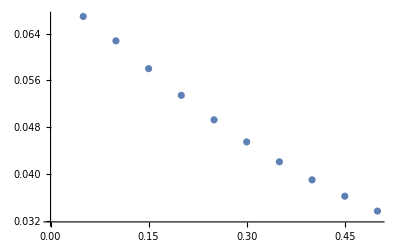

```mathematica
J=1;temp=0.0001;delta=0.1;
ListPlot[Table[{0.05i,delta ds3band[J,0.05i,delta]},{i,1,10}]]
```

```mathematica
J=1;temp=0.0001;delta=0.1;
ListPlot[Table[{0.05i,ds3bandtemp[J,0.05i,delta,temp]},{i,1,10}]]
```

-Graphics-

the two completely match!

## compound secant to find Tc

### Def: 1-dim secant method

```mathematica
bkteq3band[J_?NumericQ,m_?NumericQ,delta_?NumericQ,temp_?NumericQ]:=
(π/8)ds3bandtemp[J,m,delta,temp]-temp
```

```mathematica
(*input two temps and return a new temp*)
bkt3bandstep[temp0_,temp1_]:=(
input0=temp0;
input1=temp1;
change1=input0;
slope=(bkteq3band[J,m,delta0,change1]-bkteq3band[J,m,delta1,input1])/(change1-input1);
output0=input1;
inverseslope=1/slope;
inversetimes=inverseslope*bkteq3band[J,m,delta1,input1];
alpha=1/(1+10Abs[inversetimes]);
(*Print["The damping factor is ",alpha];*)
output1=input1-alpha*inversetimes;
)
```

```mathematica
bkt3bandsecant[inputtemp_]:=(
alpha=0.1;
output1=inputtemp;
output0=output1+0.001;
(*when the damping factor is greater than 0.95, stop the iteration*)
While[alpha<0.99,
temp=output0;
(*always using T=0 delta as starting trial*)
secant3band[delta,delta];
delta0=(2deltaA+deltaB)/3;
temp=output1;
secant3band[delta,delta];
delta1=(2deltaA+deltaB)/3;
bkt3bandstep[output0,output1];];
tempfinal=output1
)
```

```mathematica
J=1;mvalue=0;delta=0.1;
uA=ua3band[J,mvalue];
uB=ub3band[J,mvalue];
m=0.1;inputtemp=0.01;
bkt3bandsecant[inputtemp]//Timing
```

{0.640625,0.0238574}

### Δ=0.01 calculation

```mathematica
{shape1,shape2}=Graphics/@{{Red,Disk[{0,0},0.1]},{RGBColor[0,0.8,1],Polygon[{{0.5,0},{0,0.5},{-0.5,0},{0,-0.5}}]}};
```

```mathematica
J=1;mvalue=0;delta=0.01;
uA=ua3band[J,mvalue];
uB=ub3band[J,mvalue];
mlist=Table[0.0025(i-1)+0.001,{i,1,21}];
inputtemp=0.004;
tbktlist={};
For[whichm=1,whichm<Length@mlist+1,whichm++,
m=mlist[[whichm]];
AppendTo[tbktlist,bkt3bandsecant[inputtemp]];
inputtemp=tempfinal;
]//Timing
datadisp=Table[{mlist[[i]],tbktlist[[i]]},{i,1,Length@mlist}];
```

{13.5938,Null}

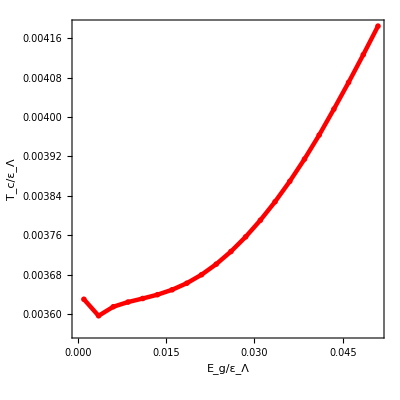

```mathematica
tcdisp=ListPlot[datadisp,
Joined->True,
PlotStyle->{{Red,Thickness[0.008]}},(*PlotRange->{{0,0.5},{0,0.025}},*)
Frame->True,FrameLabel->{Style["E_g/ε_Λ",23],Style["T_c/ε_Λ",23]},
FrameStyle->Directive[Thickness[0.007]],
(*FrameTicks->{{{0.005,0.01,0.015,0.02},None},{{0,0.1,0.2,0.3,0.4,0.5},None}},*)
LabelStyle->Directive[Black, 22],
PlotMarkers->{{shape1,0.03}},
(*PlotLegends->Placed[LineLegend[{Style["Δ=0.1ε_Λ",18]}],{0.78,0.9}],*)
AspectRatio->1,ImageSize->400,ImagePadding->100]
```

```mathematica
deltaA
```

0.00885132

```mathematica
deltaB
```

0.0177323

```mathematica
uA
uB
```

0.492895

12.6927

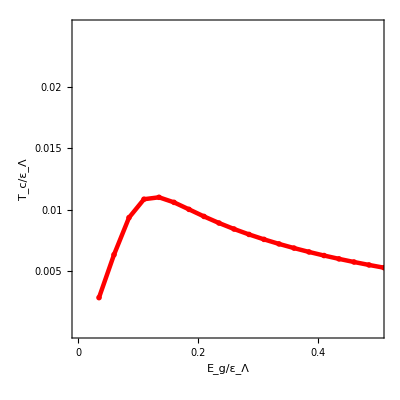
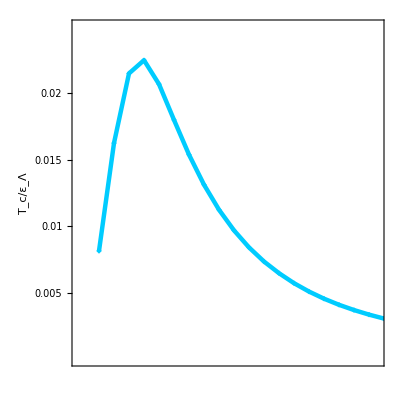

```mathematica
tcplot=Overlay[{tc01,tc05}]
```

```mathematica
Export["tc3bandf.pdf",tcplot]
```

tc3bandf.pdf